```mathematica
ClearAll[fourierSeriesGraphics]
fourierSeriesCoordinates[numberCircles_,radiusList_List,frequencyList_List]:=
With[{protoList=MapThread[{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}]},
Plus@@@Table[protoList[[;;n]],
{n,1,Length[protoList]}]//Prepend[{0,0}]]

fourierSeriesGraphics[numberCircles_,radiusList_List,frequencyList_List]:=With[{coordinateList=Partition[fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],2,1],protoList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],circleList=Apply[,]},
Print[coordinateList];

Animate[
Graphics[
{#1,#2}],{time,0,2*Pi},AnimationRunning->False]&@Evaluate[(Line[#1]&/@coordinateList),(Circle[#1]&/@protoList)]
]
```

```mathematica
ClearAll[fourierSeriesGraphicsV2]
fourierSeriesCoordinates[numberCircles_,radiusList_List,frequencyList_List]:=
	With[
		{protoList=MapThread[
						{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}
					]
				},
		Plus@@@Table[protoList[[;;n]],
		{n,1,Length[protoList]}]//Prepend[{0,0}]
]

fourierSeriesGraphicsV2[numberCircles_,radiusList_List,frequencyList_List]:=
	With[
		{
			coordinateList=Append[fourierSeriesCoordinates[numberCircles,radiusList,frequencyList]],
			protoList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],
			circleList=Evaluate[
					MapThread[
						Circle,{
							Drop[fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],-1],
							radiusList}
						]
					]
		},

	Animate[
		Graphics[{#1,#2}],
	{time,0,2*Pi},
	AnimationRunning->False]&@Evaluate[
		(Line[coordinateList]),(circleList)
	]
]
```

```mathematica
ClearAll[fourierSeriesGraphicsV2]
fourierSeriesCoordinates[numberCircles_,radiusList_List,frequencyList_List]:=
	With[
		{protoList=MapThread[
						{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}
					]
				},
		Plus@@@Table[protoList[[;;n]],
		{n,1,Length[protoList]}]//Prepend[{0,0}]
]

fourierSeriesGraphicsV2[numberCircles_,radiusList_List,frequencyList_List]:=
	With[
		{
			coordinateList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],
			protoList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],
			circleList=Evaluate[
					MapThread[
						Circle,{
							Drop[fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],-1],
							radiusList}
						]
					]
		},
	Print[coordinateList];

	Animate[
		Graphics[{#1,#2}],
	{time,0,2*Pi},
	AnimationRunning->False]&@Evaluate[
		(Line[coordinateList]),(circleList)
	]
]
```

```mathematica
ClearAll[fourierSeriesGraphicsV3]
fourierSeriesCoordinates[numberCircles_,radiusList_List,frequencyList_List]:=
	With[
		{protoList=MapThread[
						{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}
					]
				},
		Plus@@@Table[protoList[[;;n]],
		{n,1,Length[protoList]}]//Prepend[{0,0}]
]

fourierSeriesGraphicsV3[numberCircles_,radiusList_List,frequencyList_List]:=
	With[
		{
			coordinateList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],
			protoList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],
			lastCoordinate=Drop[Apply[List,
				MapThread[
						Circle,{
							Drop[
								fourierSeriesCoordinates[10,Reverse[Range[10]],Range[10]],-1],
							Reverse[Range[10]]}
						]//Last],-1][[1,2]],
			circleList=Evaluate[
					MapThread[
						Circle,{
							Drop[fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],-1],
							radiusList}
						]
					]
		},

	Animate[
		Graphics[{#1,#2,Line[Last[coordinateList],{Total[radiusList]+10,lastCoordinate}]}],
	{time,0,2*Pi},
	AnimationRunning->False]&@Evaluate[
		(Line[coordinateList]),(circleList)
	]
]
```

If the resulting wave functions are cosine then they are simple but if it is a Sine function, then it will be a +(Pi/2) to the inside of each

```mathematica
fourierSeriesGraphicsV2[5,{5,3,2,1,0.5},{1,2,4,6,8}]
```

{{0,0},{5 Cos[time],5 Sin[time]},{5 Cos[time]+3 Cos[2 time],5 Sin[time]+3 Sin[2 time]},{5 Cos[time]+3 Cos[2 time]+2 Cos[4 time],5 Sin[time]+3 Sin[2 time]+2 Sin[4 time]},{5 Cos[time]+3 Cos[2 time]+2 Cos[4 time]+Cos[6 time],5 Sin[time]+3 Sin[2 time]+2 Sin[4 time]+Sin[6 time]},{5 Cos[time]+3 Cos[2 time]+2 Cos[4 time]+Cos[6 time]+0.5 Cos[8 time],5 Sin[time]+3 Sin[2 time]+2 Sin[4 time]+Sin[6 time]+0.5 Sin[8 time]}}

```mathematica
Drop[Apply[List,MapThread[
						Circle,{
							Drop[fourierSeriesCoordinates[10,Reverse[Range[10]],Range[10]],-1],
							Reverse[Range[10]]}
						]//Last],-1][[1,2]]
```

10 Sin[time]+9 Sin[2 time]+8 Sin[3 time]+7 Sin[4 time]+6 Sin[5 time]+5 Sin[6 time]+4 Sin[7 time]+3 Sin[8 time]+2 Sin[9 time]

```mathematica
FourierSeries[(2(x)^2)+1x,x,2]//ComplexExpand/.HoldPattern[Plus]->List
```

(2 π^2)/3-8 Cos[x]+2 Cos[2 x]+2 Sin[x]-Sin[2 x]

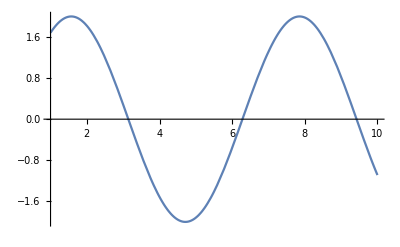

```mathematica
Plot[2 Sin[x],{x,1,10}]
```

```mathematica
Plot[2Cos]
```

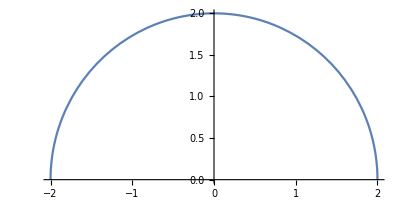
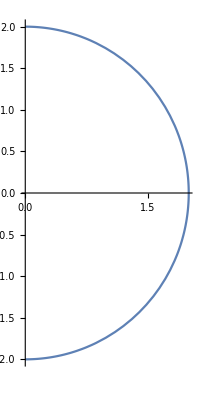

```mathematica
{ParametricPlot[#,{x,0,Pi}],ParametricPlot[Reverse@#,{x,0,Pi}]}&@{2Cos[x],2Sin[x]}
```

```mathematica
Animate[Graphics[ {Line[{{0,0},{-8 Cos[x],-8 Sin[x]}}],Circle[{0,0},8]}],{x,0,2Pi}]
```

```mathematica
Animate[Graphics[ {Line[{{0,0},{2 Cos[x+(Pi/2)],2 Sin[x+(Pi/2)]}}],Circle[{0,0},2]}],{x,0,2Pi},AnimationRunning->False]
```

```mathematica
Apply[List,FourierSeries[(2(x)^2)+1x,x,2]//ComplexExpand]
```

{(2 π^2)/3,-8 Cos[x],2 Cos[2 x],2 Sin[x],-Sin[2 x]}

```mathematica
(2 π^2)/3-8 Cos[x]+2 Cos[2 x]-8/9 Cos[3 x]+2 Sin[x]-Sin[2 x]+2/3 Sin[3 x]
```

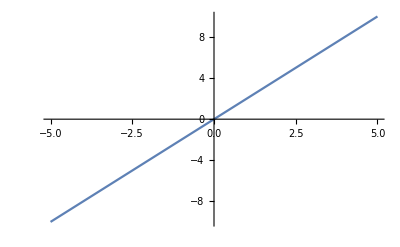

```mathematica
Plot[2x,{x,-5,5},PlotRange->{-10,10}]
```

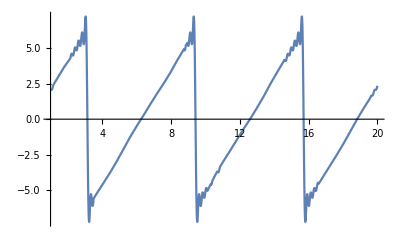

```mathematica
Plot[#1,{x,1,20},PlotRange->Full]&@Evaluate[FourierSeries[2x,x,30]//ComplexExpand]
```

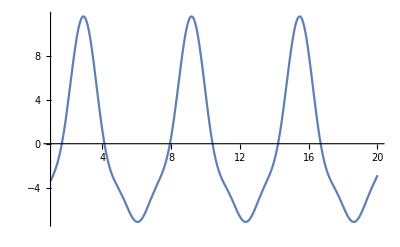

```mathematica
Plot[#1,{x,1,20},PlotRange->Full]&@( -8Cos[x]+2 Cos[2 x]-8/9 Cos[3 x]+2 Sin[x]-Sin[2 x]+2/3 Sin[3 x])
```

```mathematica
FunctionPeriod[FourierSeries[2x,x,20]//ComplexExpand,x]
```

2 π

```mathematica
ClearAll[fourierInput]

fourierInput[inputFunction_,variableUsing_,numberOfTerms_Integer]:=
With[
	{protoSeries=FourierSeries[inputFunction,variableUsing,numberOfTerms]//ComplexExpand
	},
Drop[Apply[List,protoSeries],1]
]
```

```mathematica
ClearAll[fourierInputV2]

fourierInputV2[inputFunction_,variableUsing_,numberOfTerms_Integer]:=
With[
	{protoSeries=FourierSeries[inputFunction,variableUsing,numberOfTerms]//ComplexExpand,
	manipulateSeries=Drop[Apply[List,FourierSeries[inputFunction,variableUsing,numberOfTerms]//ComplexExpand],1],
	protoCoordinateSeries={
				{
					Select[Drop[Apply[List,FourierSeries[inputFunction,variableUsing,numberOfTerms]//ComplexExpand],1],!FreeQ[#,Cos]&],
					Select[Drop[Apply[List,FourierSeries[inputFunction,variableUsing,numberOfTerms]//ComplexExpand],1],!FreeQ[#,Cos]&]/.Cos->Sin
				},
				{
					Select[Drop[Apply[List,FourierSeries[inputFunction,variableUsing,numberOfTerms]//ComplexExpand],1],!FreeQ[#,Sin]&],
					Select[Drop[Apply[List,FourierSeries[inputFunction,variableUsing,numberOfTerms]//ComplexExpand],1],!FreeQ[#,Sin]&]/.Sin->Cos
				}
			}

	},
Print[manipulateSeries];
	
		
			{
				{
					Select[manipulateSeries,!FreeQ[#,Cos]&],
					Select[manipulateSeries,!FreeQ[#,Cos]&]/.Cos->Sin
				},
				{
					Select[manipulateSeries,!FreeQ[#,Sin]&],
					Select[manipulateSeries,!FreeQ[#,Sin]&]/.Sin->Cos
				}
			}
		
]
fourierCoordinate[inputFunction_,variableUsing_,numberOfTerms_Integer]:=
MapThread[List,#]&/@fourierInputV2[inputFunction,variableUsing,numberOfTerms]
```

```mathematica
?ReplaceAll
```

```mathematica
FourierSeries[x^2,x,5]//ComplexExpand
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]

```mathematica
?Take
```

```mathematica
}
```

```mathematica
fourierInputV2[(2(x)^2)+1x,x,2]
```

{-8 Cos[x],2 Cos[2 x],2 Sin[x],-Sin[2 x]}

{{{-8 Cos[x],2 Cos[2 x]},{-8 Sin[x],2 Sin[2 x]}},{{2 Sin[x],-Sin[2 x]},{2 Cos[x],-Cos[2 x]}}}

```mathematica
{{{-8 Cos[x],2 Cos[2 x]},{-8 Sin[x],2 Sin[2 x]}},{{2 Sin[x],-Sin[2 x]},{2 Cos[x],-Cos[2 x]}}}[[1]]
```

{{-8 Cos[x],2 Cos[2 x]},{-8 Sin[x],2 Sin[2 x]}}

```mathematica
MapThread[List,#]&/@{{{-8 Cos[x],2 Cos[2 x]},{-8 Sin[x],2 Sin[2 x]}},{{2 Sin[x],-Sin[2 x]},{2 Cos[x],-Cos[2 x]}}}
```

{{{-8 Cos[x],-8 Sin[x]},{2 Cos[2 x],2 Sin[2 x]}},{{2 Sin[x],2 Cos[x]},{-Sin[2 x],-Cos[2 x]}}}

```mathematica
{{{-8 Cos[x],-8 Sin[x]},{2 Cos[2 x],2 Sin[2 x]}},{{2 Sin[x],2 Cos[x]},{-Sin[2 x],-Cos[2 x]}}}//Flatten
```

{-8 Cos[x],-8 Sin[x],2 Cos[2 x],2 Sin[2 x],2 Sin[x],2 Cos[x],-Sin[2 x],-Cos[2 x]}

```mathematica
Partition[{-8 Cos[x],-8 Sin[x],2 Cos[2 x],2 Sin[2 x],2 Sin[x],2 Cos[x],-Sin[2 x],-Cos[2 x]},2]
```

{{-8 Cos[x],-8 Sin[x]},{2 Cos[2 x],2 Sin[2 x]},{2 Sin[x],2 Cos[x]},{-Sin[2 x],-Cos[2 x]}}

```mathematica
Part
```

```mathematica
Select[List[Times[-8,Cos[x]],Times[2,Cos[Times[2,x]]],Times[2,Sin[x]],Times[-1,Sin[Times[2,x]]]],!FreeQ[#,Cos]&]
```

{-8 Cos[x],2 Cos[2 x]}

```mathematica
MapThread[List,#]&/@fourierInputV2[(2(x)^2)+1x,x,2]
```

{-8 Cos[x],2 Cos[2 x],2 Sin[x],-Sin[2 x]}

{{{-8 Cos[x],-8 Sin[x]},{2 Cos[2 x],2 Sin[2 x]}},{{2 Sin[x],2 Cos[x]},{-Sin[2 x],-Cos[2 x]}}}

```mathematica
fourierInput[((x)^2)+1x,x,2]
```

With::lvws: Variable Null$ in local variable specification {protoSeries$=ComplexExpand[FourierSeries[x+x^2,x,2]],manipulateSeries$=Drop[List@@ComplexExpand[FourierSeries[x+Power[«2»],x,2]],1],Null$} requires a value.

With[{protoSeries$=ComplexExpand[FourierSeries[x+x^2,x,2]],manipulateSeries$=Drop[List@@ComplexExpand[FourierSeries[x+x^2,x,2]],1],Null$},Print[manipulateSeries$];cosSeries=Take[manipulateSeries$,2];sinSeries=Take[manipulateSeries$,Negative[2]];Print[cosSeries];Print[sinSeries]]

```mathematica
FourierSeries[x^2,x,2]//ComplexExpand
```

π^2/3-4 Cos[x]+Cos[2 x]

```mathematica
E^(I*x)//ComplexExpand
```

Cos[x]+ⅈ Sin[x]

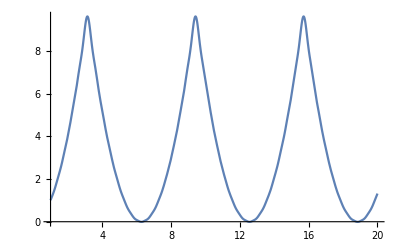

```mathematica
Plot[#1,{x,1,20},PlotRange->Full]&@(FourierSeries[x^2,x,15]//ComplexExpand)
```

```mathematica
?Map
```

```mathematica
?Cases
```

```mathematica
Cases[fourierInput[((x)^2)+1x,x,1],]
```

{}

```mathematica
?Pattern
```